```mathematica
wpe[n_]:=Sqrt[n q^2/(m ϵ0)];
(*wce[Z_]:=Abs[Z] q b0 /m;*)
ζ[vTh_,k_,ω_]:=ω/(k vTh);
Z[x_]:= I Sqrt[Pi] Exp[-x^2] Erfc[-I x];
(*Z[x_]:= I Sqrt[Pi] Exp[-x^2] (1+Erfi[-I x/I]/I);*)
Zp[x_]:=-2 (1+x Z[x]);
K3[vTh_,k_,ω_,n_]=FullSimplify[1-wpe[n]^2/(ω k vTh) Sum[BesselI[b,0] ζ[vTh,k,ω] Zp[ζ[vTh,k,ω]],{b,0,0}]];
sig33[vTh_,ω_,k_,n_]=Simplify[-(K3[vTh,k,ω,n]-1) I ω ϵ0]
stixP[n_]:=1-wpe[n]^2/ω^2;
sig33Cold[n_]:=-(stixP[n]-1) I ω ϵ0
vTh[someeV_]:=Sqrt[2 someeV eCharge/m];
```

-(2 ⅈ n q^2 ω (k vTh+ⅈ ⅇ^(-ω^2/(k^2 vTh^2)) √π ω Erfc[-(ⅈ ω)/(k vTh)]))/(k^3 m vTh^3)

```mathematica
x[v_,t_]:=v t+x0;
eField[v_,t_,E0_]:= E0 Exp[-I (k x[v,t]+ω t )];
v1[v_,nRF_,rfPeriod_,E0_]=Module[{t},q/m Integrate[eField[v,t,E0],{t,-nRF rfPeriod,0}]]
v1Indef[v_,E0_]=Module[{t},q/m Integrate[eField[v,t,E0],{t,-Infinity,0},Assumptions->{k∈Reals,v∈Reals,Im[ω]>0}]]
(*v1[v_,nRF_,rfPeriod_,E0_]:=-I (-1+Exp[I nRF rfPeriod (k v +ω)]) E0 q /(m (k v +ω));
v1Indef[v_,E0_]:=I E0 q/(m(k v + ω));*)
f[v_,vTh_,n_]= n/(vTh Sqrt[Pi]) Exp[-v^2/vTh^2];
f1[v_,vTh_,n_,nRF_,rfPeriod_,E0_]=-v1[v,nRF,rfPeriod,E0] D[f[v,vTh,n],v]
f1Indef[v_,vTh_,n_,E0_]=-v1Indef [v,E0]D[f[v,vTh,n],v]
j[n_,vTh_,nRF_,rfPeriod_,E0_,nvTh_,nvPts_]:=Module[{v},q NIntegrate[ v f1[v,vTh,n,nRF,rfPeriod,E0],{v,-nvTh vTh,nvTh vTh},AccuracyGoal->3,Method->{"TrapezoidalRule","RombergQuadrature"->False}]]
jIndef[n_,vTh_,E0_]=Module[{v},q Integrate[v f1Indef[v,vTh,n,E0],{v,-Infinity,Infinity},Assumptions->{k∈Reals,v∈Reals,Im[ω]>0,Re[ω]>0,vTh∈Reals,vTh>0,Abs[k]>0}]]
(*sig33Dlg=FullSimplify[jIndef[n,vTh,1],Assumptions->{Im[k/ω]>0}]*)
```

-(ⅈ ⅇ^(-ⅈ k x0) (-1+ⅇ^(ⅈ nRF rfPeriod (k v+ω))) E0 q)/(m (k v+ω))

(ⅈ ⅇ^(-ⅈ k x0) E0 q)/(m (k v+ω))

-(2 ⅈ ⅇ^(-v^2/vTh^2-ⅈ k x0) (-1+ⅇ^(ⅈ nRF rfPeriod (k v+ω))) E0 n q v)/(m √π vTh^3 (k v+ω))

(2 ⅈ ⅇ^(-v^2/vTh^2-ⅈ k x0) E0 n q v)/(m √π vTh^3 (k v+ω))

1/(k^3 m √π vTh^3)2 ⅈ ⅇ^(-ⅈ k x0) E0 n q^2 ω (-k √π vTh+ⅇ^(-ω^2/(k^2 vTh^2)) ω (π Erfi[ω/(k vTh)]-Log[-k/ω]+Log[k/ω]))

```mathematica
f1[1,vTh[500],1,1,1,1,4]
```

f1[1,10 √10 √(eCharge/m),1,1,1,1,4]

```mathematica
sig33[vTh,ω,ϵ0,k,n,m,q]
FullSimplify[ sig33Dlg/sig33[vTh,ω,ϵ0,k,n,m,q],,Assumptions->{k∈Reals,v∈Reals,Im[ω]>0,Re[ω]>0,vTh∈Reals,vTh>0,Abs[k]>0,Im[k/ω]>0}]
```

sig33[vTh,ω,ϵ0,k,n,m,q]

sig33Dlg/sig33[vTh,ω,ϵ0,k,n,m,q]

3.26805×10^7

1.32621×10^7

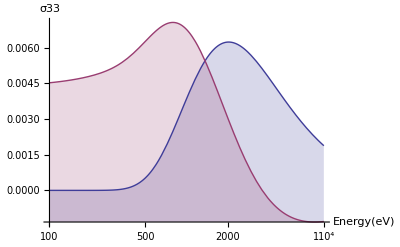

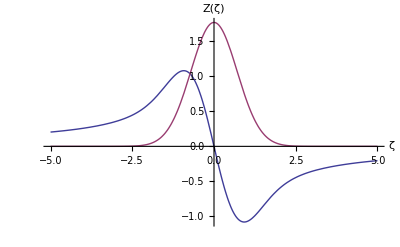

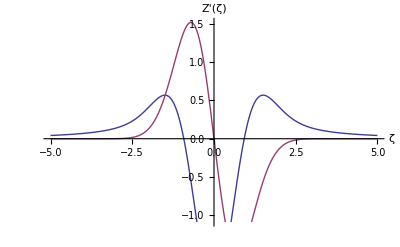

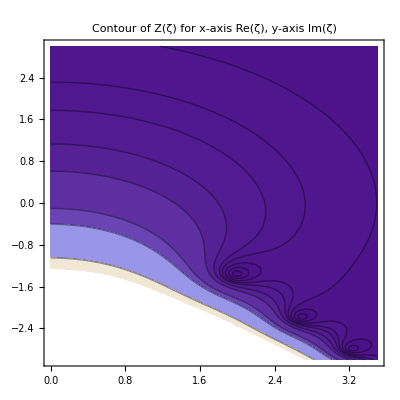

{{100,5.03056×10^-8},{200,2.90744×10^-7},{300,0.0000197832},{500,0.000524801},{800,0.00252742},{1000,0.00386322},{1500,0.00578545},{2000,0.00623294},{3000,0.00562758},{4000,0.00470758},{5000,0.00392069},{6000,0.00330023},{7000,0.00281527},{10000,0.00187793}}

{{100,0.00452167},{200,0.00480789},{300,0.0051957},{500,0.00626381},{800,0.00705783},{1000,0.00675727},{1500,0.0048779},{2000,0.00302467},{3000,0.000709186},{4000,-0.000390557},{5000,-0.000916727},{6000,-0.00116881},{7000,-0.00128293},{10000,-0.00130757}}

sig33_mathematica.nc

```mathematica
eCharge=1.60217646 10^-19; m=9.10938188 10^-31;
q=-eCharge;
freq=1.15 10^8;
E0=5000;
rfPeriod=1/freq;
x0=101.3;

n=1.1 10^14;
k = 22.11;
nRF =5;
ω=2 Pi freq +I 2 Pi freq 1 10^-5;
vPhs=Re[ω/k]
tPhs=0.5 m vPhs^2/eCharge;
kPer=0;
vTh[500]
λ=2 Pi /k;
ϵ0=8.854187817 10^-12;

LogLinearPlot[{Re[sig33[vTh[EeV],ω,k,n]],Im[sig33[vTh[EeV],ω,k,n]]},{EeV,100,10000},Filling->Axis,AxesLabel->{Energy [eV],σ33}]
Plot[{Re[Z[x]],Im[Z[x]]},{x,-5,5},AxesLabel->{"ζ","Z(ζ)"}]
Plot[{Re[Zp[x]],Im[Zp[x]]},{x,-5,5},AxesLabel->{"ζ","Z'(ζ)"}]
ContourPlot[Abs[Z[x+I y]],{x,0,3.5},{y,-3.0,3.0},Contours->{0.1,0.2,0.3,0.4,0.5,0.7,1.0,2.0,3.0,10.0,100.0},PlotLabel->"Contour of Z(ζ) for x-axis Re(ζ), y-axis Im(ζ)"]
tValsZ={100,200,300,500,800,1000,1500,2000,3000,4000,5000,6000,7000,10000};
reValsZ= Table[{rteV,Re[sig33[vTh[rteV],ω,k,n]]},{rteV,tValsZ}]
imValsZ= Table[{rteV,Im[sig33[vTh[rteV],ω,k,n]]},{rteV,tValsZ}]
Export["sig33_mathematica.nc",{reValsZ,imValsZ},"NetCDF"]
```

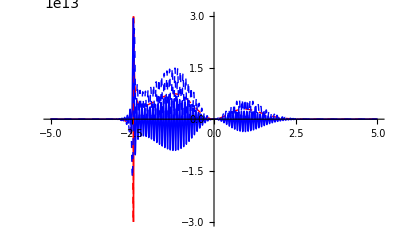

```mathematica
thiseV=500;
thisnRF=30;
thisnvTh=5;
Plot[{Re[thisv vTh[thiseV] f1Indef[thisv vTh[thiseV],vTh[thiseV],n,E0]] ,
Im[thisv vTh[thiseV] f1Indef[thisv vTh[thiseV],vTh[thiseV],n,E0]],
Re[thisv vTh[thiseV] f1[thisv vTh[thiseV],vTh[thiseV],n,thisnRF,rfPeriod,E0]],Im[thisv vTh[thiseV]f1[thisv vTh[thiseV],vTh[thiseV],n,thisnRF,rfPeriod,E0]]},{thisv,-thisnvTh ,thisnvTh},PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed,Thick],Blue,Directive[Blue,Dashed]},PlotRange->0.3 10^14]
```

```mathematica
thisnRF=30;
thisnvTh=5;
thiseV=500;
thisnPts=500;
nStepsPerCycle=55;
nSteps=thisnRF*nStepsPerCycle+1;
dt=-rfPeriod/nStepsPerCycle;
tGrid[i_]:=(i-1) dt;
tList=Array[tGrid,nSteps];
```

```mathematica
vRange=vTh[thiseV]thisnvTh 2;
vMin=-vRange/2;
vSize=vRange/thisnPts;
vGrid[i_]:=(i-1) vSize+vMin+vSize/2;
vList=Array[vGrid,thisnPts];
vList;
```

```mathematica
x[vList[[1]],tList];
```

```mathematica
eField[vList[[1]],tList,E0];
```

```mathematica
v1[vList,thisnRF,rfPeriod,E0];
```

```mathematica
j[n,vTh[thiseV],thisnRF,rfPeriod,E0,thisnvTh,thisnPts]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v$12797 near {v$12797} = {-3.24104×10^7}. NIntegrate obtained -2.51249×10^19 + 1.9465×10^20\ ⅈ and 1.87686×10^18 for the integral and error estimates.

4.02546-31.1864 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in v near {v} = {3.97862×10^7}. NIntegrate obtained 1.09997×10^14 and 2.37534×10^9 for the integral and error estimates.

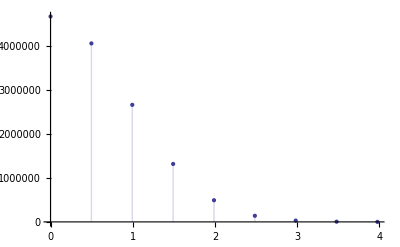

```mathematica
ListPlot[Last[Reap[NIntegrate[  f[v,vTh[500],n],{v,-3 vTh[500],3 vTh[500]},Method->{"TrapezoidalRule","RombergQuadrature"->False},MaxRecursion->0,MaxPoints->10,EvaluationMonitor:>Sow[{v,f[v,vTh[500],n]}]]]],Filling->0]
```

```mathematica
thiseV=500;
thisnRF=5;
thisnvTh=5;
thisnPts=500;
j[n,vTh[thiseV],thisnRF,rfPeriod,E0,thisnvTh,thisnPts]
jIndef[n,vTh[thiseV],E0]
```

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained -2.52426×10^19 + 1.94535×10^20\ ⅈ and 1.98796×10^18 for the integral and error estimates.

4.04431-31.1679 ⅈ

4.04227-31.1677 ⅈ

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained -8.26262×10^15 - 1.41134×10^20\ ⅈ and 1.15782×10^18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained 4.4498×10^15 - 1.50099×10^20\ ⅈ and 2.03459×10^18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained -5.90829×10^17 - 1.6214×10^20\ ⅈ and 2.70983×10^18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained -1.635×10^19 - 1.9552×10^20\ ⅈ and 2.21133×10^18 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained -8.26262×10^15 - 1.41134×10^20\ ⅈ and 1.15782×10^18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained 4.4498×10^15 - 1.50099×10^20\ ⅈ and 2.03459×10^18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained -5.90829×10^17 - 1.6214×10^20\ ⅈ and 2.70983×10^18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 501 integrand evaluations. NIntegrate obtained -1.635×10^19 - 1.9552×10^20\ ⅈ and 2.21133×10^18 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

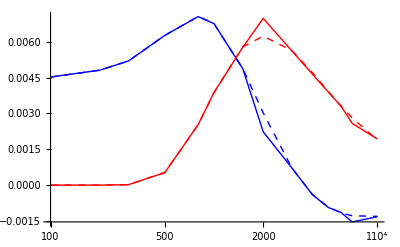

```mathematica
tVals={100,200,300,500,800,1000,1500,2000,3000,4000,5000,6000,7000,10000};
thisnRF =10;
thisnvTh = 4;
thisnPts=500;
reVals= Table[{rteV,
Re[j[n,vTh[rteV],thisnRF,rfPeriod,E0,thisnvTh,thisnPts]/eField[0,0,E0] ]},{rteV,tVals}];
imVals=Table[{rteV,
Im[j[n,vTh[rteV],thisnRF,rfPeriod,E0,thisnvTh,thisnPts]/eField[0,0,E0]]},{rteV,tVals}];
ListLogLinearPlot[{reVals,imVals,reValsZ,imValsZ},PlotStyle->{Red,Blue,Directive[Red,Dashed],Directive[Blue,Dashed]},Joined->True]
```